```mathematica
σ0[r_]:=1-0.9 ⅇ^(-(r/10)^2)
```

```mathematica
ρ=30;
eps=10^-3;
FB=ParametricNDSolve[{
u'[r]==-(ϵ+σ0[r])v[r],
v'[r]==-2/r v[r]+(ϵ-σ0[r])u[r],
u[ρ]==((1+ϵ)ρ)/(1+√(1-ϵ^2)ρ)v[ρ],
(*u[eps]==eps/3(σ0^2-ϵ^2)u0,*)
(*v[eps]==eps/3(ϵ-σ0[0])uin,*)
u[eps]==uin+eps^2/2-1/2(ϵ+σ0[0])
},
{u,v},{r,eps,ρ},{ϵ,uin}]
```

{u→ParametricFunction[<>],v→ParametricFunction[<>]}

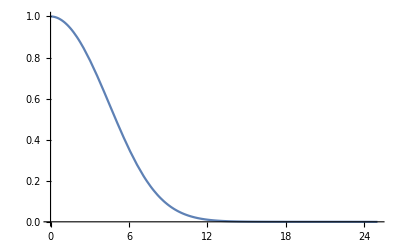

```mathematica
Plot[u[0.40273851,1][r]/.FB,{r,0.001,25}]
```

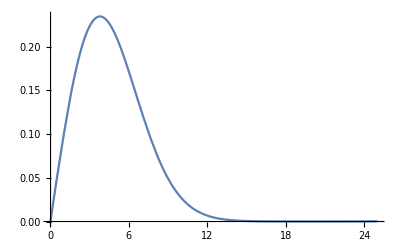

```mathematica
Plot[v[0.40273851,1][r]/.FB,{r,0.01,25}]
```

```mathematica
ρ=30;
eps=10^-3;
FB=ParametricNDSolve[{
u'[r]==-(ϵ+σ0[r])v[r],
v'[r]==-2/r v[r]+(ϵ-σ0[r])u[r],
u[ρ]==((1+ϵ)ρ)/(1+√(1-ϵ^2)ρ)v[ρ],
(*u[eps]==eps/3(σ0^2-ϵ^2)u0,*)
(*v[eps]==eps/3(ϵ-σ0[0])uin,*)
u[eps]==uin+eps^2/2-1/2(ϵ+σ0[0])
},
{u,v},{r,eps,ρ},{ϵ,uin}]
```

```mathematica
DSolve[y''[r]+2/r y'[r]-m^2 y[r]==0,y,r]
```

{{y→Function[{r},(ⅇ^(-m r) C[1])/r+(ⅇ^(m r) C[2])/(2 m r)]}}

```mathematica
FS[ϵ_,R_,n_]:=(
h=R/n;
veq[-1]=v[-1]+4v[0]+v[1]==0;
veq[0]=-1/(2h)(v[-1]-v[1])==1/h(v[-1]-v[1])+(ϵ-σ0[0])1/6(4u[0]+2u[1]);
Table[veq[i]=-1/(2h)(v[i-1]-v[i+1])==-2/(i h)1/6(v[i-1]+4v[i]+v[i+1])+(ϵ-σ0[i h])1/6(u[i-1]+4u[i]+u[i+1]),{i,1,n-1}];
veq[n]=-1/(2h)v[n-1]==-2/R 1/6(v[n-1]+4v[n])+(ϵ-σ0[R])1/6(u[n-1]+4u[n]+u[n+1]);
(*ueq[0]=-1/(2h)(u[-1]-u[1])==-(ϵ+σ0[0])1/6(v[-1]+4v[0]+v[1]);*)
Table[ueq[i]=-1/(2h)(u[i-1]-u[i+1])==-(ϵ+σ0[i h])1/6(v[i-1]+4v[i]+v[i+1]),{i,1,n-1}];
(*ueq[n]=-1/(2h)(u[n-1]-u[n+1])==-(ϵ+σ0[R])1/6(v[n-1]+4v[n]);*)
ueq[0]=2 1/6 u[1]+2/3 u[0]==1;
ueq[n+1]=(1/6(√(1-ϵ^2)+1/R)-1/(2h))u[n-1]+2/3(√(1-ϵ^2)+1/R)u[n]+(1/6(√(1-ϵ^2)+1/R)+1/(2 h))u[n+1]==0;
equations=Join[Table[veq[i],{i,-1,n}],Table[ueq[i],{i,0,n+1}]];
vars=Join[Table[u[k],{k,0,n+1}],Table[v[k],{k,-1,n}]];
sol=NSolve[equations,vars,Reals];
Vcoeff=Table[v[i],{i,-1,n}]/.sol;
Ucoeff=Table[u[i],{i,0,n+1}]/.sol;
)
```

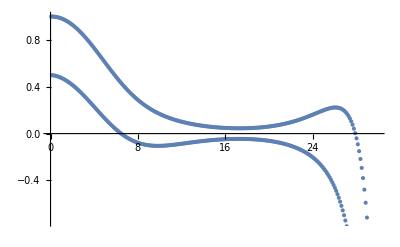

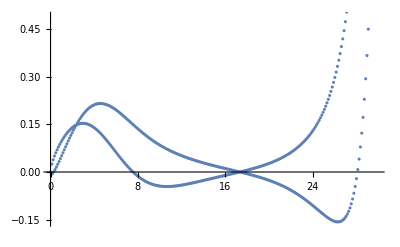

```mathematica
FS[0.40273851,30,500]
ListPlot[Table[{k h,1/6(Ucoeff[[1,1+k]]+4Ucoeff[[1,2+k]]+Ucoeff[[1,3+k]])},{k,1,499}]]
ListPlot[Table[{k h,1/6(Vcoeff[[1,1+k]]+4Vcoeff[[1,2+k]]+Vcoeff[[1,3+k]])},{k,0,499}]]
```

```mathematica
Vcoeff[[1]]
```

{-0.0378219,0.0158836,-0.0257124,0.0552151,-0.0408377,0.0796582,-0.043619,0.0973492,-0.0413115,0.111137,-0.0359419,0.122245,-0.0284775,0.131334,-0.0194874,0.138806,-0.00934899,0.144927,0.00166679,0.149886,0.0133542,0.153818,0.02555,0.156828,0.0381206,0.158998,0.0509538,0.160393,0.0639532,0.161066,0.0770352,0.161062,0.090126,0.160419,0.10316,0.159172,0.116079,0.157349,0.128831,0.154978,0.141367,0.152084,0.153646,0.148693,0.16563,0.144825,0.177283,0.140506,0.188575,0.135755,0.19948,0.130596,0.209972,0.12505,0.220032,0.11914,0.229641,0.112889,0.238784,0.106319,0.247448,0.0994537,0.255624,0.0923166,0.263303,0.0849317,0.270482,0.0773235,0.277156,0.0695167,0.283325,0.0615361,0.28899,0.0534071,0.294154,0.0451548,0.298821,0.0368047,0.302999,0.0283821,0.306695,0.0199122,0.309917,0.0114201,0.312677,0.00293059,0.314987,-0.00553204,0.316858,-0.0139439,0.318304,-0.0222816,0.31934,-0.0305226,0.319981,-0.038645,0.320241,-0.0466276,0.320137,-0.0544505,0.319685,-0.0620943,0.318901,-0.0695411,0.317801,-0.0767738,0.316403,-0.0837766,0.314722,-0.0905349,0.312774,-0.0970352,0.310576,-0.103266,0.308143,-0.109215,0.30549,-0.114874,0.302633,-0.120235,0.299585,-0.12529,0.296361,-0.130033,0.292973,-0.134461,0.289435,-0.138571,0.28576,-0.142359,0.281957,-0.145826,0.27804,-0.148971,0.274017,-0.151797,0.269899,-0.154304,0.265696,-0.156497,0.261415,-0.15838,0.257065,-0.159957,0.252653,-0.161235,0.248187,-0.162219,0.243673,-0.162916,0.239116,-0.163335,0.234523,-0.163483,0.229898,-0.163368,0.225247,-0.163,0.220573,-0.162386,0.21588,-0.161537,0.211171,-0.160462,0.206451,-0.15917,0.201721,-0.15767,0.196985,-0.155973,0.192245,-0.154088,0.187502,-0.152024,0.182759,-0.14979,0.178016,-0.147396,0.173277,-0.144851,0.168541,-0.142162,0.16381,-0.139338,0.159085,-0.136389,0.154365,-0.13332,0.149653,-0.13014,0.144948,-0.126856,0.14025,-0.123474,0.13556,-0.120002,0.130877,-0.116444,0.126201,-0.112807,0.121532,-0.109096,0.116869,-0.105315,0.112213,-0.10147,0.107561,-0.0975639,0.102913,-0.0936005,0.0982687,-0.0895833,0.0936262,-0.0855151,0.0889844,-0.0813985,0.0843419,-0.0772355,0.079697,-0.073028,0.075048,-0.0687773,0.0703932,-0.0644845,0.0657303,-0.0601503,0.0610573,-0.055775,0.0563719,-0.0513585,0.0516714,-0.0469006,0.0469534,-0.0424006,0.0422148,-0.0378575,0.0374528,-0.03327,0.0326642,-0.0286364,0.0278456,-0.0239549,0.0229935,-0.0192232,0.0181042,-0.0144389,0.0131739,-0.00959899,0.00819851,-0.00470052,0.00317371,0.000259952,-0.0019049,0.00528607,-0.00704197,0.0103818,-0.0122423,0.0155513,-0.0175111,0.0207992,-0.0228534,0.0261302,-0.0282748,0.0315494,-0.033781,0.037062,-0.0393779,0.0426738,-0.0450716,0.0483907,-0.0508685,0.0542187,-0.0567751,0.0601644,-0.0627985,0.0662346,-0.0689455,0.0724363,-0.0752237,0.0787769,-0.0816407,0.0852641,-0.0882042,0.0919058,-0.0949226,0.0987104,-0.101804,0.105687,-0.108858,0.112843,-0.116093,0.12019,-0.123518,0.127736,-0.131143,0.135491,-0.138979,0.143467,-0.147035,0.151674,-0.155323,0.160123,-0.163852,0.168826,-0.172636,0.177795,-0.181685,0.187042,-0.191013,0.196582,-0.20063,0.206426,-0.210552,0.21659,-0.220791,0.227089,-0.23136,0.237936,-0.242276,0.249149,-0.253552,0.260743,-0.265204,0.272736,-0.277247,0.285145,-0.289699,0.297989,-0.302576,0.311287,-0.315896,0.325059,-0.329676,0.339325,-0.343936,0.354108,-0.358695,0.369429,-0.373972,0.385313,-0.389788,0.401783,-0.406163,0.418866,-0.423121,0.436587,-0.440682,0.454974,-0.45887,0.474057,-0.477709,0.493865,-0.497223,0.514431,-0.517437,0.535786,-0.538376,0.557966,-0.560067,0.581006,-0.582537,0.604945,-0.605813,0.629822,-0.629923,0.655679,-0.654897,0.682559,-0.680764,0.710508,-0.707553,0.739574,-0.735296,0.769807,-0.764023,0.801262,-0.793765,0.833993,-0.824555,0.868059,-0.856423,0.903524,-0.889402,0.940452,-0.923525,0.978913,-0.958823,1.01898,-0.995328,1.06073,-1.03307,1.10425,-1.07208,1.14962,-1.1124,1.19694,-1.15404,1.24631,-1.19703,1.29782,-1.24141,1.3516,-1.2872,1.40776,-1.33441,1.46643,-1.38307,1.52774,-1.43319,1.59185,-1.48478,1.6589,-1.53785,1.72907,-1.5924,1.80253,-1.64843,1.87948,-1.70592,1.96013,-1.76485,2.04469,-1.82519,2.13343,-1.8869,2.22658,-1.94993,2.32445,-2.01421,2.42733,-2.07965,2.53555,-2.14616,2.64949,-2.21362,2.76952,-2.28187,2.89608,-2.35075,3.02963,-2.42006,3.17067,-2.48956,3.31976,-2.559,3.47749,-2.62805,3.64453,-2.69637,3.82159,-2.76353,4.00947,-2.82909,4.20901,-2.8925,4.42117,-2.95315,4.64699,-3.01037,4.8876,-3.06337,5.14425,-3.11127,5.41833,-3.15307,5.71134,-3.18765,6.02494,-3.21374,6.36099,-3.22992,6.72149,-3.23459,7.10868,-3.22593,7.52503,-3.20192,7.97324,-3.16029,8.45632,-3.09848,8.97758,-3.01365,9.54069,-2.90259,10.1497,-2.76171,10.8091,-2.58701,11.5238,-2.374,12.2993,-2.11765,13.1417,-1.81237,14.0578,-1.45189,15.0549,-1.02921,16.1414,-0.536513,17.3263}

```mathematica
sol
```

{{u[0]→1.5,u[1]→-1.42553×10^-13,u[2]→1.50032,u[3]→-0.00155195,u[4]→1.50061,u[5]→-0.00390897,u[6]→1.50058,u[7]→-0.00697741,u[8]→1.50014,u[9]→-0.0106857,u[10]→1.49924,u[11]→-0.014982,u[12]→1.49782,u[13]→-0.0198263,u[14]→1.49587,u[15]→-0.0251856,u[16]→1.49336,u[17]→-0.0310317,u[18]→1.49027,u[19]→-0.0373393,u[20]→1.4866,u[21]→-0.0440852,u[22]→1.48233,u[23]→-0.0512477,u[24]→1.47746,u[25]→-0.0588059,u[26]→1.47199,u[27]→-0.0667395,u[28]→1.46592,u[29]→-0.0750284,u[30]→1.45924,u[31]→-0.0836526,u[32]→1.45197,u[33]→-0.0925919,u[34]→1.4441,u[35]→-0.101826,u[36]→1.43564,u[37]→-0.111334,u[38]→1.4266,u[39]→-0.121096,u[40]→1.41699,u[41]→-0.131089,u[42]→1.40682,u[43]→-0.141292,u[44]→1.3961,u[45]→-0.151682,u[46]→1.38484,u[47]→-0.162237,u[48]→1.37306,u[49]→-0.172932,u[50]→1.36077,u[51]→-0.183745,u[52]→1.348,u[53]→-0.194652,u[54]→1.33474,u[55]→-0.205626,u[56]→1.32104,u[57]→-0.216644,u[58]→1.3069,u[59]→-0.22768,u[60]→1.29234,u[61]→-0.23871,u[62]→1.27739,u[63]→-0.249707,u[64]→1.26207,u[65]→-0.260645,u[66]→1.2464,u[67]→-0.2715,u[68]→1.23041,u[69]→-0.282246,u[70]→1.21411,u[71]→-0.292858,u[72]→1.19753,u[73]→-0.303311,u[74]→1.18071,u[75]→-0.313581,u[76]→1.16365,u[77]→-0.323643,u[78]→1.14639,u[79]→-0.333476,u[80]→1.12895,u[81]→-0.343056,u[82]→1.11136,u[83]→-0.352361,u[84]→1.09364,u[85]→-0.361372,u[86]→1.07581,u[87]→-0.370068,u[88]→1.0579,u[89]→-0.378431,u[90]→1.03994,u[91]→-0.386443,u[92]→1.02195,u[93]→-0.394089,u[94]→1.00394,u[95]→-0.401354,u[96]→0.985949,u[97]→-0.408224,u[98]→0.96799,u[99]→-0.414688,u[100]→0.950085,u[101]→-0.420735,u[102]→0.932254,u[103]→-0.426356,u[104]→0.914516,u[105]→-0.431544,u[106]→0.896888,u[107]→-0.436293,u[108]→0.879389,u[109]→-0.440599,u[110]→0.862033,u[111]→-0.444459,u[112]→0.844837,u[113]→-0.447872,u[114]→0.827813,u[115]→-0.450838,u[116]→0.810976,u[117]→-0.45336,u[118]→0.794337,u[119]→-0.45544,u[120]→0.777907,u[121]→-0.457083,u[122]→0.761696,u[123]→-0.458296,u[124]→0.745713,u[125]→-0.459085,u[126]→0.729967,u[127]→-0.459459,u[128]→0.714463,u[129]→-0.459428,u[130]→0.699209,u[131]→-0.459002,u[132]→0.68421,u[133]→-0.458194,u[134]→0.669471,u[135]→-0.457016,u[136]→0.654995,u[137]→-0.455481,u[138]→0.640785,u[139]→-0.453603,u[140]→0.626845,u[141]→-0.451398,u[142]→0.613175,u[143]→-0.448881,u[144]→0.599777,u[145]→-0.446068,u[146]→0.586651,u[147]→-0.442975,u[148]→0.573799,u[149]→-0.439619,u[150]→0.56122,u[151]→-0.436017,u[152]→0.548912,u[153]→-0.432185,u[154]→0.536877,u[155]→-0.428141,u[156]→0.525111,u[157]→-0.423902,u[158]→0.513615,u[159]→-0.419485,u[160]→0.502386,u[161]→-0.414908,u[162]→0.491422,u[163]→-0.410186,u[164]→0.480723,u[165]→-0.405337,u[166]→0.470285,u[167]→-0.400378,u[168]→0.460107,u[169]→-0.395323,u[170]→0.450186,u[171]→-0.39019,u[172]→0.440522,u[173]→-0.384994,u[174]→0.43111,u[175]→-0.379748,u[176]→0.421951,u[177]→-0.37447,u[178]→0.41304,u[179]→-0.369171,u[180]→0.404378,u[181]→-0.363867,u[182]→0.395961,u[183]→-0.35857,u[184]→0.387788,u[185]→-0.353293,u[186]→0.379858,u[187]→-0.348049,u[188]→0.372168,u[189]→-0.342849,u[190]→0.364718,u[191]→-0.337705,u[192]→0.357506,u[193]→-0.332628,u[194]→0.350531,u[195]→-0.327628,u[196]→0.343792,u[197]→-0.322715,u[198]→0.337289,u[199]→-0.317899,u[200]→0.331019,u[201]→-0.313189,u[202]→0.324983,u[203]→-0.308594,u[204]→0.31918,u[205]→-0.304122,u[206]→0.31361,u[207]→-0.29978,u[208]→0.308273,u[209]→-0.295577,u[210]→0.303169,u[211]→-0.29152,u[212]→0.298297,u[213]→-0.287616,u[214]→0.293659,u[215]→-0.283871,u[216]→0.289254,u[217]→-0.280293,u[218]→0.285083,u[219]→-0.276886,u[220]→0.281146,u[221]→-0.273656,u[222]→0.277445,u[223]→-0.270611,u[224]→0.273981,u[225]→-0.267754,u[226]→0.270755,u[227]→-0.265092,u[228]→0.267768,u[229]→-0.26263,u[230]→0.265022,u[231]→-0.260372,u[232]→0.262518,u[233]→-0.258324,u[234]→0.260258,u[235]→-0.256491,u[236]→0.258244,u[237]→-0.254877,u[238]→0.256479,u[239]→-0.253487,u[240]→0.254965,u[241]→-0.252327,u[242]→0.253705,u[243]→-0.251401,u[244]→0.252701,u[245]→-0.250714,u[246]→0.251956,u[247]→-0.250271,u[248]→0.251475,u[249]→-0.250078,u[250]→0.251259,u[251]→-0.250138,u[252]→0.251313,u[253]→-0.250458,u[254]→0.251641,u[255]→-0.251043,u[256]→0.252248,u[257]→-0.251898,u[258]→0.253137,u[259]→-0.253029,u[260]→0.254313,u[261]→-0.254443,u[262]→0.255782,u[263]→-0.256145,u[264]→0.257549,u[265]→-0.258142,u[266]→0.259619,u[267]→-0.26044,u[268]→0.261999,u[269]→-0.263046,u[270]→0.264694,u[271]→-0.265968,u[272]→0.267712,u[273]→-0.269213,u[274]→0.27106,u[275]→-0.272789,u[276]→0.274744,u[277]→-0.276704,u[278]→0.278774,u[279]→-0.280968,u[280]→0.283156,u[281]→-0.285588,u[282]→0.287899,u[283]→-0.290574,u[284]→0.293013,u[285]→-0.295937,u[286]→0.298507,u[287]→-0.301686,u[288]→0.304391,u[289]→-0.307832,u[290]→0.310675,u[291]→-0.314387,u[292]→0.317371,u[293]→-0.321363,u[294]→0.324489,u[295]→-0.328771,u[296]→0.332041,u[297]→-0.336626,u[298]→0.340041,u[299]→-0.34494,u[300]→0.348501,u[301]→-0.353728,u[302]→0.357435,u[303]→-0.363005,u[304]→0.366856,u[305]→-0.372786,u[306]→0.37678,u[307]→-0.383087,u[308]→0.387223,u[309]→-0.393926,u[310]→0.3982,u[311]→-0.405321,u[312]→0.409728,u[313]→-0.41729,u[314]→0.421826,u[315]→-0.429853,u[316]→0.43451,u[317]→-0.44303,u[318]→0.4478,u[319]→-0.456842,u[320]→0.461715,u[321]→-0.471312,u[322]→0.476277,u[323]→-0.486464,u[324]→0.491506,u[325]→-0.502321,u[326]→0.507425,u[327]→-0.51891,u[328]→0.524056,u[329]→-0.536257,u[330]→0.541424,u[331]→-0.554389,u[332]→0.559553,u[333]→-0.573337,u[334]→0.578468,u[335]→-0.593131,u[336]→0.598197,u[337]→-0.613803,u[338]→0.618766,u[339]→-0.635386,u[340]→0.640204,u[341]→-0.657916,u[342]→0.66254,u[343]→-0.68143,u[344]→0.685804,u[345]→-0.705965,u[346]→0.710029,u[347]→-0.731563,u[348]→0.735245,u[349]→-0.758265,u[350]→0.761487,u[351]→-0.786115,u[352]→0.788788,u[353]→-0.815161,u[354]→0.817184,u[355]→-0.845451,u[356]→0.846711,u[357]→-0.877036,u[358]→0.877406,u[359]→-0.90997,u[360]→0.909307,u[361]→-0.944309,u[362]→0.942453,u[363]→-0.980112,u[364]→0.976885,u[365]→-1.01744,u[366]→1.01264,u[367]→-1.05636,u[368]→1.04977,u[369]→-1.09695,u[370]→1.0883,u[371]→-1.13927,u[372]→1.12829,u[373]→-1.1834,u[374]→1.16977,u[375]→-1.22942,u[376]→1.2128,u[377]→-1.27741,u[378]→1.2574,u[379]→-1.32748,u[380]→1.30364,u[381]→-1.37971,u[382]→1.35155,u[383]→-1.4342,u[384]→1.40118,u[385]→-1.49106,u[386]→1.45257,u[387]→-1.55041,u[388]→1.50576,u[389]→-1.61236,u[390]→1.5608,u[391]→-1.67704,u[392]→1.61773,u[393]→-1.7446,u[394]→1.67658,u[395]→-1.81516,u[396]→1.7374,u[397]→-1.8889,u[398]→1.80021,u[399]→-1.96596,u[400]→1.86506,u[401]→-2.04653,u[402]→1.93196,u[403]→-2.1308,u[404]→2.00095,u[405]→-2.21897,u[406]→2.07203,u[407]→-2.31124,u[408]→2.14522,u[409]→-2.40786,u[410]→2.22052,u[411]→-2.50907,u[412]→2.29794,u[413]→-2.61513,u[414]→2.37745,u[415]→-2.72634,u[416]→2.45903,u[417]→-2.843,u[418]→2.54264,u[419]→-2.96545,u[420]→2.62824,u[421]→-3.09404,u[422]→2.71575,u[423]→-3.22916,u[424]→2.80509,u[425]→-3.37125,u[426]→2.89614,u[427]→-3.52074,u[428]→2.98878,u[429]→-3.67814,u[430]→3.08284,u[431]→-3.84399,u[432]→3.17814,u[433]→-4.01886,u[434]→3.27445,u[435]→-4.2034,u[436]→3.3715,u[437]→-4.3983,u[438]→3.46899,u[439]→-4.6043,u[440]→3.56656,u[441]→-4.82224,u[442]→3.66379,u[443]→-5.05302,u[444]→3.76021,u[445]→-5.29761,u[446]→3.85528,u[447]→-5.55709,u[448]→3.94835,u[449]→-5.83264,u[450]→4.03874,u[451]→-6.12555,u[452]→4.12561,u[453]→-6.43723,u[454]→4.20805,u[455]→-6.76925,u[456]→4.28502,u[457]→-7.1233,u[458]→4.35532,u[459]→-7.50125,u[460]→4.41763,u[461]→-7.90518,u[462]→4.47043,u[463]→-8.33735,u[464]→4.51201,u[465]→-8.80025,u[466]→4.54046,u[467]→-9.29665,u[468]→4.55361,u[469]→-9.82957,u[470]→4.54905,u[471]→-10.4024,u[472]→4.52403,u[473]→-11.0187,u[474]→4.47551,u[475]→-11.6827,u[476]→4.40004,u[477]→-12.3988,u[478]→4.29378,u[479]→-13.1721,u[480]→4.1524,u[481]→-14.0079,u[482]→3.9711,u[483]→-14.9124,u[484]→3.74445,u[485]→-15.8924,u[486]→3.46641,u[487]→-16.9552,u[488]→3.13022,u[489]→-18.109,u[490]→2.72832,u[491]→-19.3631,u[492]→2.25227,u[493]→-20.7275,u[494]→1.69263,u[495]→-22.2133,u[496]→1.03888,u[497]→-23.833,u[498]→0.279235,u[499]→-25.6003,u[500]→-0.599415,u[501]→-24.6023,v[-1]→-0.0378219,v[0]→0.0158836,v[1]→-0.0257124,v[2]→0.0552151,v[3]→-0.0408377,v[4]→0.0796582,v[5]→-0.043619,v[6]→0.0973492,v[7]→-0.0413115,v[8]→0.111137,v[9]→-0.0359419,v[10]→0.122245,v[11]→-0.0284775,v[12]→0.131334,v[13]→-0.0194874,v[14]→0.138806,v[15]→-0.00934899,v[16]→0.144927,v[17]→0.00166679,v[18]→0.149886,v[19]→0.0133542,v[20]→0.153818,v[21]→0.02555,v[22]→0.156828,v[23]→0.0381206,v[24]→0.158998,v[25]→0.0509538,v[26]→0.160393,v[27]→0.0639532,v[28]→0.161066,v[29]→0.0770352,v[30]→0.161062,v[31]→0.090126,v[32]→0.160419,v[33]→0.10316,v[34]→0.159172,v[35]→0.116079,v[36]→0.157349,v[37]→0.128831,v[38]→0.154978,v[39]→0.141367,v[40]→0.152084,v[41]→0.153646,v[42]→0.148693,v[43]→0.16563,v[44]→0.144825,v[45]→0.177283,v[46]→0.140506,v[47]→0.188575,v[48]→0.135755,v[49]→0.19948,v[50]→0.130596,v[51]→0.209972,v[52]→0.12505,v[53]→0.220032,v[54]→0.11914,v[55]→0.229641,v[56]→0.112889,v[57]→0.238784,v[58]→0.106319,v[59]→0.247448,v[60]→0.0994537,v[61]→0.255624,v[62]→0.0923166,v[63]→0.263303,v[64]→0.0849317,v[65]→0.270482,v[66]→0.0773235,v[67]→0.277156,v[68]→0.0695167,v[69]→0.283325,v[70]→0.0615361,v[71]→0.28899,v[72]→0.0534071,v[73]→0.294154,v[74]→0.0451548,v[75]→0.298821,v[76]→0.0368047,v[77]→0.302999,v[78]→0.0283821,v[79]→0.306695,v[80]→0.0199122,v[81]→0.309917,v[82]→0.0114201,v[83]→0.312677,v[84]→0.00293059,v[85]→0.314987,v[86]→-0.00553204,v[87]→0.316858,v[88]→-0.0139439,v[89]→0.318304,v[90]→-0.0222816,v[91]→0.31934,v[92]→-0.0305226,v[93]→0.319981,v[94]→-0.038645,v[95]→0.320241,v[96]→-0.0466276,v[97]→0.320137,v[98]→-0.0544505,v[99]→0.319685,v[100]→-0.0620943,v[101]→0.318901,v[102]→-0.0695411,v[103]→0.317801,v[104]→-0.0767738,v[105]→0.316403,v[106]→-0.0837766,v[107]→0.314722,v[108]→-0.0905349,v[109]→0.312774,v[110]→-0.0970352,v[111]→0.310576,v[112]→-0.103266,v[113]→0.308143,v[114]→-0.109215,v[115]→0.30549,v[116]→-0.114874,v[117]→0.302633,v[118]→-0.120235,v[119]→0.299585,v[120]→-0.12529,v[121]→0.296361,v[122]→-0.130033,v[123]→0.292973,v[124]→-0.134461,v[125]→0.289435,v[126]→-0.138571,v[127]→0.28576,v[128]→-0.142359,v[129]→0.281957,v[130]→-0.145826,v[131]→0.27804,v[132]→-0.148971,v[133]→0.274017,v[134]→-0.151797,v[135]→0.269899,v[136]→-0.154304,v[137]→0.265696,v[138]→-0.156497,v[139]→0.261415,v[140]→-0.15838,v[141]→0.257065,v[142]→-0.159957,v[143]→0.252653,v[144]→-0.161235,v[145]→0.248187,v[146]→-0.162219,v[147]→0.243673,v[148]→-0.162916,v[149]→0.239116,v[150]→-0.163335,v[151]→0.234523,v[152]→-0.163483,v[153]→0.229898,v[154]→-0.163368,v[155]→0.225247,v[156]→-0.163,v[157]→0.220573,v[158]→-0.162386,v[159]→0.21588,v[160]→-0.161537,v[161]→0.211171,v[162]→-0.160462,v[163]→0.206451,v[164]→-0.15917,v[165]→0.201721,v[166]→-0.15767,v[167]→0.196985,v[168]→-0.155973,v[169]→0.192245,v[170]→-0.154088,v[171]→0.187502,v[172]→-0.152024,v[173]→0.182759,v[174]→-0.14979,v[175]→0.178016,v[176]→-0.147396,v[177]→0.173277,v[178]→-0.144851,v[179]→0.168541,v[180]→-0.142162,v[181]→0.16381,v[182]→-0.139338,v[183]→0.159085,v[184]→-0.136389,v[185]→0.154365,v[186]→-0.13332,v[187]→0.149653,v[188]→-0.13014,v[189]→0.144948,v[190]→-0.126856,v[191]→0.14025,v[192]→-0.123474,v[193]→0.13556,v[194]→-0.120002,v[195]→0.130877,v[196]→-0.116444,v[197]→0.126201,v[198]→-0.112807,v[199]→0.121532,v[200]→-0.109096,v[201]→0.116869,v[202]→-0.105315,v[203]→0.112213,v[204]→-0.10147,v[205]→0.107561,v[206]→-0.0975639,v[207]→0.102913,v[208]→-0.0936005,v[209]→0.0982687,v[210]→-0.0895833,v[211]→0.0936262,v[212]→-0.0855151,v[213]→0.0889844,v[214]→-0.0813985,v[215]→0.0843419,v[216]→-0.0772355,v[217]→0.079697,v[218]→-0.073028,v[219]→0.075048,v[220]→-0.0687773,v[221]→0.0703932,v[222]→-0.0644845,v[223]→0.0657303,v[224]→-0.0601503,v[225]→0.0610573,v[226]→-0.055775,v[227]→0.0563719,v[228]→-0.0513585,v[229]→0.0516714,v[230]→-0.0469006,v[231]→0.0469534,v[232]→-0.0424006,v[233]→0.0422148,v[234]→-0.0378575,v[235]→0.0374528,v[236]→-0.03327,v[237]→0.0326642,v[238]→-0.0286364,v[239]→0.0278456,v[240]→-0.0239549,v[241]→0.0229935,v[242]→-0.0192232,v[243]→0.0181042,v[244]→-0.0144389,v[245]→0.0131739,v[246]→-0.00959899,v[247]→0.00819851,v[248]→-0.00470052,v[249]→0.00317371,v[250]→0.000259952,v[251]→-0.0019049,v[252]→0.00528607,v[253]→-0.00704197,v[254]→0.0103818,v[255]→-0.0122423,v[256]→0.0155513,v[257]→-0.0175111,v[258]→0.0207992,v[259]→-0.0228534,v[260]→0.0261302,v[261]→-0.0282748,v[262]→0.0315494,v[263]→-0.033781,v[264]→0.037062,v[265]→-0.0393779,v[266]→0.0426738,v[267]→-0.0450716,v[268]→0.0483907,v[269]→-0.0508685,v[270]→0.0542187,v[271]→-0.0567751,v[272]→0.0601644,v[273]→-0.0627985,v[274]→0.0662346,v[275]→-0.0689455,v[276]→0.0724363,v[277]→-0.0752237,v[278]→0.0787769,v[279]→-0.0816407,v[280]→0.0852641,v[281]→-0.0882042,v[282]→0.0919058,v[283]→-0.0949226,v[284]→0.0987104,v[285]→-0.101804,v[286]→0.105687,v[287]→-0.108858,v[288]→0.112843,v[289]→-0.116093,v[290]→0.12019,v[291]→-0.123518,v[292]→0.127736,v[293]→-0.131143,v[294]→0.135491,v[295]→-0.138979,v[296]→0.143467,v[297]→-0.147035,v[298]→0.151674,v[299]→-0.155323,v[300]→0.160123,v[301]→-0.163852,v[302]→0.168826,v[303]→-0.172636,v[304]→0.177795,v[305]→-0.181685,v[306]→0.187042,v[307]→-0.191013,v[308]→0.196582,v[309]→-0.20063,v[310]→0.206426,v[311]→-0.210552,v[312]→0.21659,v[313]→-0.220791,v[314]→0.227089,v[315]→-0.23136,v[316]→0.237936,v[317]→-0.242276,v[318]→0.249149,v[319]→-0.253552,v[320]→0.260743,v[321]→-0.265204,v[322]→0.272736,v[323]→-0.277247,v[324]→0.285145,v[325]→-0.289699,v[326]→0.297989,v[327]→-0.302576,v[328]→0.311287,v[329]→-0.315896,v[330]→0.325059,v[331]→-0.329676,v[332]→0.339325,v[333]→-0.343936,v[334]→0.354108,v[335]→-0.358695,v[336]→0.369429,v[337]→-0.373972,v[338]→0.385313,v[339]→-0.389788,v[340]→0.401783,v[341]→-0.406163,v[342]→0.418866,v[343]→-0.423121,v[344]→0.436587,v[345]→-0.440682,v[346]→0.454974,v[347]→-0.45887,v[348]→0.474057,v[349]→-0.477709,v[350]→0.493865,v[351]→-0.497223,v[352]→0.514431,v[353]→-0.517437,v[354]→0.535786,v[355]→-0.538376,v[356]→0.557966,v[357]→-0.560067,v[358]→0.581006,v[359]→-0.582537,v[360]→0.604945,v[361]→-0.605813,v[362]→0.629822,v[363]→-0.629923,v[364]→0.655679,v[365]→-0.654897,v[366]→0.682559,v[367]→-0.680764,v[368]→0.710508,v[369]→-0.707553,v[370]→0.739574,v[371]→-0.735296,v[372]→0.769807,v[373]→-0.764023,v[374]→0.801262,v[375]→-0.793765,v[376]→0.833993,v[377]→-0.824555,v[378]→0.868059,v[379]→-0.856423,v[380]→0.903524,v[381]→-0.889402,v[382]→0.940452,v[383]→-0.923525,v[384]→0.978913,v[385]→-0.958823,v[386]→1.01898,v[387]→-0.995328,v[388]→1.06073,v[389]→-1.03307,v[390]→1.10425,v[391]→-1.07208,v[392]→1.14962,v[393]→-1.1124,v[394]→1.19694,v[395]→-1.15404,v[396]→1.24631,v[397]→-1.19703,v[398]→1.29782,v[399]→-1.24141,v[400]→1.3516,v[401]→-1.2872,v[402]→1.40776,v[403]→-1.33441,v[404]→1.46643,v[405]→-1.38307,v[406]→1.52774,v[407]→-1.43319,v[408]→1.59185,v[409]→-1.48478,v[410]→1.6589,v[411]→-1.53785,v[412]→1.72907,v[413]→-1.5924,v[414]→1.80253,v[415]→-1.64843,v[416]→1.87948,v[417]→-1.70592,v[418]→1.96013,v[419]→-1.76485,v[420]→2.04469,v[421]→-1.82519,v[422]→2.13343,v[423]→-1.8869,v[424]→2.22658,v[425]→-1.94993,v[426]→2.32445,v[427]→-2.01421,v[428]→2.42733,v[429]→-2.07965,v[430]→2.53555,v[431]→-2.14616,v[432]→2.64949,v[433]→-2.21362,v[434]→2.76952,v[435]→-2.28187,v[436]→2.89608,v[437]→-2.35075,v[438]→3.02963,v[439]→-2.42006,v[440]→3.17067,v[441]→-2.48956,v[442]→3.31976,v[443]→-2.559,v[444]→3.47749,v[445]→-2.62805,v[446]→3.64453,v[447]→-2.69637,v[448]→3.82159,v[449]→-2.76353,v[450]→4.00947,v[451]→-2.82909,v[452]→4.20901,v[453]→-2.8925,v[454]→4.42117,v[455]→-2.95315,v[456]→4.64699,v[457]→-3.01037,v[458]→4.8876,v[459]→-3.06337,v[460]→5.14425,v[461]→-3.11127,v[462]→5.41833,v[463]→-3.15307,v[464]→5.71134,v[465]→-3.18765,v[466]→6.02494,v[467]→-3.21374,v[468]→6.36099,v[469]→-3.22992,v[470]→6.72149,v[471]→-3.23459,v[472]→7.10868,v[473]→-3.22593,v[474]→7.52503,v[475]→-3.20192,v[476]→7.97324,v[477]→-3.16029,v[478]→8.45632,v[479]→-3.09848,v[480]→8.97758,v[481]→-3.01365,v[482]→9.54069,v[483]→-2.90259,v[484]→10.1497,v[485]→-2.76171,v[486]→10.8091,v[487]→-2.58701,v[488]→11.5238,v[489]→-2.374,v[490]→12.2993,v[491]→-2.11765,v[492]→13.1417,v[493]→-1.81237,v[494]→14.0578,v[495]→-1.45189,v[496]→15.0549,v[497]→-1.02921,v[498]→16.1414,v[499]→-0.536513,v[500]→17.3263}}